# Slepton-side γ-radiation

## Load FeynCalc

```mathematica
description="Photon radiation correction to slepton pair production.";
If[$FrontEnd===Null,
$FeynCalcStartupMessages=False;
Print[description];
];
If[$Notebooks===False,
$FeynCalcStartupMessages=False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Calculate the squared amplitude

### Draw diagrams

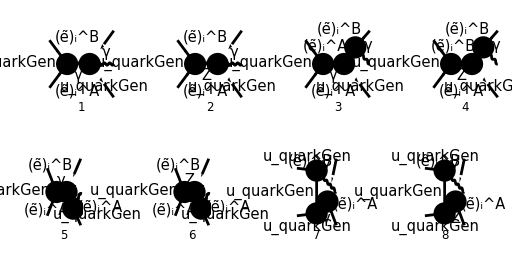

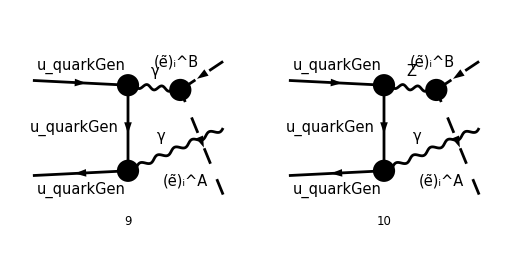

```mathematica
diags=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4]}
];
Paint[
diags,
ColumnsXRows->{4,2},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[p3, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(3\)]\)"; 
MakeBoxes[p4, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(4\)]\)";
```

```mathematica
M[0]=FCFAConvert[
CreateFeynAmp[diags],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{p3,k,p4},
ChangeDimension->4,
UndoChiralSplittings->True,
(*List->False,*) (*NB! Messes with ordering of diagrams!*)
Contract->True,
DropSumOver->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{-(4 (φ(-OverBar[p_2])).(γ̄·(ε̄)^*(k)).(φ(OverBar[p_1])) IndexDelta(A,B) e^3 δ_Col1Col2)/(3 (k̄+OverBar[p_3]+OverBar[p_4])^2),(ⅈ (φ(-OverBar[p_2])).((2 ⅈ (γ̄·(ε̄)^*(k)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ̄·(ε̄)^*(k)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(((k̄+OverBar[p_3]+OverBar[p_4])^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(2 (φ(-OverBar[p_2])).(γ̄·(k̄+OverBar[p_3]-OverBar[p_4])).(φ(OverBar[p_1])) IndexDelta(A,B) (-(k̄·(ε̄)^*(k))-2 (OverBar[p_3]·(ε̄)^*(k))) e^3 δ_Col1Col2)/(3 (k̄+OverBar[p_3]+OverBar[p_4])^2 ((-k̄-OverBar[p_3])^2-(MSf(A,2,i))^2)),(ⅈ (φ(-OverBar[p_2])).((2 ⅈ (γ̄·(k̄+OverBar[p_3]-OverBar[p_4])).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ̄·(k̄+OverBar[p_3]-OverBar[p_4])).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])) (-(k̄·(ε̄)^*(k))-2 (OverBar[p_3]·(ε̄)^*(k))) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((-k̄-OverBar[p_3])^2-(MSf(B,2,i))^2) ((k̄+OverBar[p_3]+OverBar[p_4])^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(2 (φ(-OverBar[p_2])).(γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(φ(OverBar[p_1])) IndexDelta(A,B) (-(k̄·(ε̄)^*(k))-2 (OverBar[p_4]·(ε̄)^*(k))) e^3 δ_Col1Col2)/(3 (k̄+OverBar[p_3]+OverBar[p_4])^2 ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2)),(ⅈ (φ(-OverBar[p_2])).((2 ⅈ (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])) (-(k̄·(ε̄)^*(k))-2 (OverBar[p_4]·(ε̄)^*(k))) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2) ((k̄+OverBar[p_3]+OverBar[p_4])^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(4 (φ(-OverBar[p_2])).(γ̄·(OverBar[p_4]-OverBar[p_3])).(γ̄·(-OverBar[p_2]+OverBar[p_3]+OverBar[p_4])).(γ̄·(ε̄)^*(k)).(φ(OverBar[p_1])) IndexDelta(A,B) e^3 δ_Col1Col2)/(9 (OverBar[p_2]-OverBar[p_3]-OverBar[p_4])^2 (OverBar[p_3]+OverBar[p_4])^2),(ⅈ (φ(-OverBar[p_2])).((2 ⅈ (γ̄·(OverBar[p_4]-OverBar[p_3])).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ̄·(OverBar[p_4]-OverBar[p_3])).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(γ̄·(-OverBar[p_2]+OverBar[p_3]+OverBar[p_4])).(γ̄·(ε̄)^*(k)).(φ(OverBar[p_1])) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(3 (OverBar[p_2]-OverBar[p_3]-OverBar[p_4])^2 ((OverBar[p_3]+OverBar[p_4])^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(4 (φ(-OverBar[p_2])).(γ̄·(ε̄)^*(k)).(γ̄·(k̄-OverBar[p_2])).(γ̄·(OverBar[p_4]-OverBar[p_3])).(φ(OverBar[p_1])) IndexDelta(A,B) e^3 δ_Col1Col2)/(9 (OverBar[p_2]-k̄)^2 (OverBar[p_3]+OverBar[p_4])^2),(ⅈ (φ(-OverBar[p_2])).(γ̄·(ε̄)^*(k)).(γ̄·(k̄-OverBar[p_2])).((2 ⅈ (γ̄·(OverBar[p_4]-OverBar[p_3])).(γ̄)^6 e (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ (γ̄·(OverBar[p_4]-OverBar[p_3])).(γ̄)^7 e (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])) e^2 δ_Col1Col2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(3 (OverBar[p_2]-k̄)^2 ((OverBar[p_3]+OverBar[p_4])^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))}

### Extract the fifth diagram, and change 2/3 to e_Q

```mathematica
Pair[Momentum[k],Momentum[Polarization[k,-I]]]=0; (*Lorenz gauge*)
M5[0]=Part[M[0],5];
M5[1]=M5[0] 3/2 SMP["e_Q"]
```

```mathematica
M5[1]//DiracSimplify
```

```mathematica
M5CC[1]=ComplexConjugate[M5[1]]
```

```mathematica
FCClearScalarProducts[];
SP[p1]=0;SP[p2]=0;SP[k]=0;
(*SetMandelstam*) (*How do I do this for a 2->3 process?*)
```

```mathematica
M5Squared[0]=(M5[1] M5CC[1])//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/(4 SUNN^2)]&//DoPolarizationSums[#,k,0]&(*//DiracSimplify//SUNSimplify[#,SUNNToCACF->False]&//Simplify*)
```

```mathematica
SP[p3]=MSf[B,2,i]^2; SP[p4]=MSf[A,2,i]^2; MSf[B,2,i]=MSf[A,2,i];
```

```mathematica
M5Squared[1]=M5Squared[0]//Simplify
```

```mathematica
Mandelstam23Rules={
Pair[Momentum[p1],Momentum[p2]]->s12/2,
Pair[Momentum[p1],Momentum[p3]]->(MSf[A,2,i]^2-t13)/2,
Pair[Momentum[p1],Momentum[p4]]->(MSf[A,2,i]^2-t14)/2,
Pair[Momentum[p2],Momentum[p3]]->(MSf[A,2,i]^2-t23)/2,
Pair[Momentum[p2],Momentum[p4]]->(MSf[A,2,i]^2-t24)/2
};
```

```mathematica
M5Squared[2]=M5Squared[1]//.Mandelstam23Rules//Simplify
```

### Extract all diagrams radiating from A-slepton

Change  to for quark charge in photon diagram.

```mathematica
M5[0]=M[0][[5]] 3/2 SMP["e_Q"]
M6[0]=M[0][[6]]
```

-(e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (-(k̄·(ε̄)^*(k))-2 (OverBar[p_4]·(ε̄)^*(k))) (φ(-OverBar[p_2])).(γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(φ(OverBar[p_1])))/((k̄+OverBar[p_3]+OverBar[p_4])^2 ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2))

(ⅈ e^2 (-(k̄·(ε̄)^*(k))-2 (OverBar[p_4]·(ε̄)^*(k))) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-OverBar[p_2])).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])))/(2 (cos(θ_W)) (sin(θ_W)) ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2) ((k̄+OverBar[p_3]+OverBar[p_4])^2-m_Z^2))

#### Extract the prefactor for photon-diagram

```mathematica
M5[1]=M5[0]/.{FeynAmpDenominator[PropagatorDenominator[Momentum[k+p4],MSf[A,2,i]]] FeynAmpDenominator[PropagatorDenominator[Momentum[k+p3+p4],0]]->PROPAGATORS}
```

e^3 (-PROPAGATORS) e_Q δ_Col1Col2 IndexDelta(A,B) (-(k̄·(ε̄)^*(k))-2 (OverBar[p_4]·(ε̄)^*(k))) (φ(-OverBar[p_2])).(γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(φ(OverBar[p_1]))

```mathematica
M5[2]=M5[1]/.{SMP["e"]^3 SMP["e_Q"] PROPAGATORS IndexDelta[A,B]->Prefacγ}//Simplify
```

Prefacγ δ_Col1Col2 (k̄·(ε̄)^*(k)+2 (OverBar[p_4]·(ε̄)^*(k))) (φ(-OverBar[p_2])).(γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(φ(OverBar[p_1]))

#### Extract the prefactor for Z-diagram

Rewrite the “chiral coefficients” into and  (see p.164 in Richardson). Note that the amplitudes in FeynArts used up quarks.

```mathematica
M6[1]=M6[0]/.{
4 SMP["sin_W"]^2-3:>12 Zql,
SMP["sin_W"]/SMP["cos_W"]:>3Zqr / (SMP["sin_W"] SMP["cos_W"])
};
```

Rewrite the sfermion mixing matrices USf into (again: see p.164 in Richardson), using that the mixing matrices are real, and .

```mathematica
M6[2]=M6[1]/.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify;
M6[3]=M6[2]/.{2 SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2ZliAB}
```

(ⅈ e^2 ZliAB (k̄·(ε̄)^*(k)+2 (OverBar[p_4]·(ε̄)^*(k))) (φ(-OverBar[p_2])).(2 ⅈ e δ_Col1Col2 (Zql (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^7+Zqr (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(OverBar[p_1])))/((cos(θ_W)) (sin(θ_W)) ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2) ((k̄+OverBar[p_3]+OverBar[p_4])^2-m_Z^2))

```mathematica
M6[4]=M6[3]//.{FeynAmpDenominator[PropagatorDenominator[Momentum[p4+k],MSf[A,2,i]]] FeynAmpDenominator[PropagatorDenominator[Momentum[k+p3+p4],SMP["m_Z"]]]->PROPAGATORS}
```

1/((cos(θ_W)) (sin(θ_W)))ⅈ e^2 PROPAGATORS ZliAB (k̄·(ε̄)^*(k)+2 (OverBar[p_4]·(ε̄)^*(k))) (φ(-OverBar[p_2])).(2 ⅈ e δ_Col1Col2 (Zql (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^7+Zqr (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(OverBar[p_1]))

```mathematica
M6[5]=M6[4]//DiracSimplify//ReplaceAll[#,{SMP["e"]^3 ZliAB PROPAGATORS/(SMP["sin_W"]^2 SMP["cos_W"]^2)->PrefacZ}]&//Simplify
```

2 PrefacZ δ_Col1Col2 (k̄·(ε̄)^*(k)+2 (OverBar[p_4]·(ε̄)^*(k))) (-Zql (φ(-OverBar[p_2])).(γ̄·(k̄+OverBar[p_4])).(γ̄)^7.(φ(OverBar[p_1]))-Zqr (φ(-OverBar[p_2])).(γ̄·(k̄+OverBar[p_4])).(γ̄)^6.(φ(OverBar[p_1]))+Zql (φ(-OverBar[p_2])).(γ̄·OverBar[p_3]).(γ̄)^7.(φ(OverBar[p_1]))+Zqr (φ(-OverBar[p_2])).(γ̄·OverBar[p_3]).(γ̄)^6.(φ(OverBar[p_1])))

#### Recombine photon- and Z-diagrams and compute square

```mathematica
Pair[Momentum[k],Momentum[Polarization[k,-I]]]=0
```

```mathematica
M56[0]=M5[2]+M6[5]
```

Prefacγ δ_Col1Col2 (k̄·(ε̄)^*(k)+2 (OverBar[p_4]·(ε̄)^*(k))) (φ(-OverBar[p_2])).(γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(φ(OverBar[p_1]))+2 PrefacZ δ_Col1Col2 (k̄·(ε̄)^*(k)+2 (OverBar[p_4]·(ε̄)^*(k))) (-Zql (φ(-OverBar[p_2])).(γ̄·(k̄+OverBar[p_4])).(γ̄)^7.(φ(OverBar[p_1]))-Zqr (φ(-OverBar[p_2])).(γ̄·(k̄+OverBar[p_4])).(γ̄)^6.(φ(OverBar[p_1]))+Zql (φ(-OverBar[p_2])).(γ̄·OverBar[p_3]).(γ̄)^7.(φ(OverBar[p_1]))+Zqr (φ(-OverBar[p_2])).(γ̄·OverBar[p_3]).(γ̄)^6.(φ(OverBar[p_1])))

```mathematica
M56CC[0]=ComplexConjugate[M56[0],Conjugate->{PrefacZ}]
```

2 Zql Conjugate[PrefacZ] δ_Col1Col2 (k̄·ε̄(k)+2 (OverBar[p_4]·ε̄(k))) (φ(OverBar[p_1])).(γ̄)^6.(γ̄·OverBar[p_3]).(φ(-OverBar[p_2]))+2 Zqr Conjugate[PrefacZ] δ_Col1Col2 (k̄·ε̄(k)+2 (OverBar[p_4]·ε̄(k))) (φ(OverBar[p_1])).(γ̄)^7.(γ̄·OverBar[p_3]).(φ(-OverBar[p_2]))-2 Zql Conjugate[PrefacZ] δ_Col1Col2 (k̄·ε̄(k)+2 (OverBar[p_4]·ε̄(k))) (φ(OverBar[p_1])).(γ̄)^6.(γ̄·(k̄+OverBar[p_4])).(φ(-OverBar[p_2]))-2 Zqr Conjugate[PrefacZ] δ_Col1Col2 (k̄·ε̄(k)+2 (OverBar[p_4]·ε̄(k))) (φ(OverBar[p_1])).(γ̄)^7.(γ̄·(k̄+OverBar[p_4])).(φ(-OverBar[p_2]))+Prefacγ δ_Col1Col2 (k̄·ε̄(k)+2 (OverBar[p_4]·ε̄(k))) (φ(OverBar[p_1])).(γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(φ(-OverBar[p_2]))

```mathematica
FCClearScalarProducts[];
SetMandelstam[x,{p1,p2,-p3,-k,-p4},{0,0,MSf[B,2,i],0,MSf[A,2,i]}];
(*SP[p1]=0;SP[p2]=0;SP[k]=0;
SP[p3]=MSf[B,2,i];SP[p4]=MSf[A,2,i];*)
```

```mathematica
M56Squared[0]=(M56[0] M56CC[0])//DiracSimplify//Simplify
```

δ_Col1Col2^2 (k̄·(ε̄)^*(k)+2 (OverBar[p_4]·(ε̄)^*(k))) (k̄·ε̄(k)+2 (OverBar[p_4]·ε̄(k))) (-Prefacγ (φ(-OverBar[p_2])).(γ̄·(k̄+OverBar[p_4])).(φ(OverBar[p_1]))+2 PrefacZ (Zql (φ(-OverBar[p_2])).(γ̄·k̄+γ̄·OverBar[p_4]).(γ̄)^7.(φ(OverBar[p_1]))+Zqr (φ(-OverBar[p_2])).(γ̄·k̄+γ̄·OverBar[p_4]).(γ̄)^6.(φ(OverBar[p_1]))-Zql (φ(-OverBar[p_2])).(γ̄·OverBar[p_3]).(γ̄)^7.(φ(OverBar[p_1]))-Zqr (φ(-OverBar[p_2])).(γ̄·OverBar[p_3]).(γ̄)^6.(φ(OverBar[p_1])))+Prefacγ (φ(-OverBar[p_2])).(γ̄·OverBar[p_3]).(φ(OverBar[p_1]))) (2 Conjugate[PrefacZ] (Zql (φ(OverBar[p_1])).(γ̄·k̄+γ̄·OverBar[p_4]).(γ̄)^7.(φ(-OverBar[p_2]))+Zqr (φ(OverBar[p_1])).(γ̄·k̄+γ̄·OverBar[p_4]).(γ̄)^6.(φ(-OverBar[p_2]))-Zql (φ(OverBar[p_1])).(γ̄·OverBar[p_3]).(γ̄)^7.(φ(-OverBar[p_2]))-Zqr (φ(OverBar[p_1])).(γ̄·OverBar[p_3]).(γ̄)^6.(φ(-OverBar[p_2])))-Prefacγ (φ(OverBar[p_1])).(γ̄·(k̄+OverBar[p_4])).(φ(-OverBar[p_2]))+Prefacγ (φ(OverBar[p_1])).(γ̄·OverBar[p_3]).(φ(-OverBar[p_2])))

```mathematica
M56Squared[1]=M56Squared[0]//FermionSpinSum[#,ExtraFactor->1/(4 SUNN^2)]&//SUNSimplify[#,SUNNToCACF->False]&//DoPolarizationSums[#,k,0]&//DiracSimplify//Simplify
```

1/N 4 ((MSf(A,2,i))^2+x(4,5)) ((x(4,5)-x(2,3)) (MSf(B,2,i))^2+x(2,3) (x(1,2)+x(2,3)-x(4,5))) (-Prefacγ Conjugate[PrefacZ] (Zql+Zqr)+2 PrefacZ Conjugate[PrefacZ] (Zql^2+Zqr^2)+Prefacγ^2-Prefacγ PrefacZ (Zql+Zqr))

```mathematica
M56Squared[2]=M56Squared[1]/.{(-Prefacγ Conjugate[PrefacZ](Zql+Zqr)-Prefacγ PrefacZ(Zql+Zqr))->-2Prefacγ Re[PrefacZ](Zql+Zqr)}
```

1/N 4 ((MSf(A,2,i))^2+x(4,5)) ((x(4,5)-x(2,3)) (MSf(B,2,i))^2+x(2,3) (x(1,2)+x(2,3)-x(4,5))) (2 PrefacZ Conjugate[PrefacZ] (Zql^2+Zqr^2)+Prefacγ^2-2 Prefacγ Re(PrefacZ) (Zql+Zqr))

```mathematica
M56Squared[3]=M56Squared[2]/.{x[4,5]->x[1,2]+x[1,3]+x[2,3]-MSf[B,2,i]^2}//Simplify
```

-1/N4 (-(x(1,2)+x(1,3)+x(2,3)) (MSf(B,2,i))^2+(MSf(B,2,i))^4+x(1,3) x(2,3)) ((MSf(A,2,i))^2-(MSf(B,2,i))^2+x(1,2)+x(1,3)+x(2,3)) (2 PrefacZ Conjugate[PrefacZ] (Zql^2+Zqr^2)+Prefacγ (Prefacγ-2 Re(PrefacZ) (Zql+Zqr)))

```mathematica
FCClearScalarProducts[];
M56Squared[4]=M56Squared[3]/.{
x[1,2]->2 SP[p1,p2],
x[1,3]->MSf[B,2,i]^2-2SP[p1,p3],
x[2,3]->MSf[B,2,i]^2-2SP[p2,p3]
}//Simplify
```

1/N 8 (2 PrefacZ Conjugate[PrefacZ] (Zql^2+Zqr^2)+Prefacγ (Prefacγ-2 Re(PrefacZ) (Zql+Zqr))) ((OverBar[p_1]·OverBar[p_2]) (MSf(B,2,i))^2-2 (OverBar[p_1]·OverBar[p_3]) (OverBar[p_2]·OverBar[p_3])) (2 (OverBar[p_1]·OverBar[p_2])-2 (OverBar[p_1]·OverBar[p_3])-2 (OverBar[p_2]·OverBar[p_3])+(MSf(A,2,i))^2+(MSf(B,2,i))^2)

### Compare with hand calculations

```mathematica
M56SquaredByHand[0]=4/SUNN (Prefacγ^2+2PrefacZ^2 (Zql^2+Zqr^2)-2Prefacγ PrefacZ (Zql+Zqr)) 4 MSf[A,2,i]^2 (MSf[B,2,i] Pair[Momentum[p1],Momentum[p2]]-2 Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[p2],Momentum[p3]])
```

```mathematica
FCCompareResults[{M56Squared[1]},{M56SquaredByHand},Text->{"Compare M56Squared to hand calculation:", "CORRECT!", "WRONG!"},Interrupt->{Hold[Quit[1]],Automatic}];
```